```mathematica
curve[x_]=c1*x^3+c2*x^2+c3*x+c4
```

```mathematica
curve[x_]=c1 x^3 + c2 x^2 +c3 x + c4
```

c4+c3 x+c2 x^2+c1 x^3

```mathematica
coefs0=Solve[{{x1,curve[x1],curve'[x1]},{x2,curve[x2],curve'[x2]}}=={{60.,2,-0.05},{94.,0.5,-0.005}},{x1,x2,c1,c2,c3,c4}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→60.,x2→94.,c1→0.0000287503,c2→-0.00597954,c3→0.357043,c4→-4.10625}}

```mathematica
coefs1=Solve[{{x1,curve[x1],curve'[x1]},{x2,curve[x2],curve'[x2]}}=={{94.,0.5,-0.005},{200.,0.2,0}},{x1,x2,c1,c2,c3,c4}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→94.,x2→200.,c1→5.87733×10^-8,c2→-2.33414×10^-6,c3→-0.00611915,c4→1.04701}}

```mathematica
coefs2=Solve[{{x1,curve[x1],curve'[x1]},{x2,curve[x2],curve'[x2]}}=={{94.,0.5,-0.005},{400.,0.2,0}},{x1,x2,c1,c2,c3,c4}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→94.,x2→400.,c1→-3.24578×10^-8,c2→0.0000322211,c3→-0.0101972,c4→1.20079}}

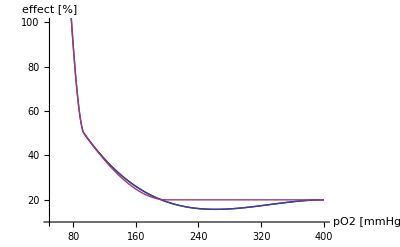

```mathematica
Show[Plot[100*curve[x]/. coefs2, {x,94,400}, PlotRange->{{50,400},{10,100}}, AxesLabel->{"pO2 [mmHg]","effect [%]"}],
Plot[{100*curve[x]/. coefs0,100*curve[x]/. coefs0}, {x,60,94}],
Plot[{100*curve[x]/. coefs2,100*curve[x]/. coefs1}, {x,94,200}],
Plot[{100*curve[x]/. coefs2,100*0.2}, {x,200,400}]]
```